```mathematica
Problem 1
```

```mathematica
x={0,4,8,12,16,20,24,28,32,36,40,44,48};yg={4,5,4,6,5,7,4,6,9,6,5,3,8};ysol={4,4.4,4.8,5.2,5.6,6,5,6.5,8,6,4,4,8};
```

```mathematica
Length[x]
```

13

```mathematica
Length[yg]
```

13

```mathematica
Length[ysol]
```

13

```mathematica
yg+1
```

{5,6,5,7,6,8,5,7,10,7,6,4,9}

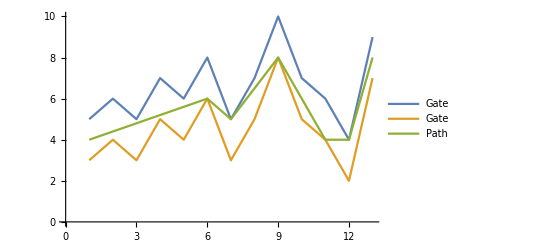

```mathematica
ListPlot[{yg+1,yg-1,ysol},Joined->True,PlotLegends->{"Gate","Gate","Path"}]
```

```mathematica
Problem 2
```

```mathematica
x={1.000,2};y={1.000,3.828};r={1,2};
```

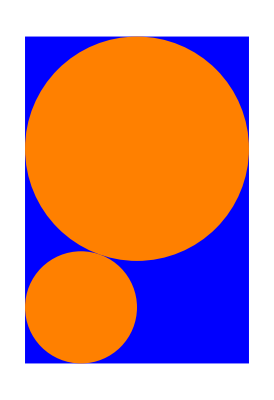

```mathematica
Graphics[{Blue,Rectangle[{0,0},{4,5.828}],Orange,Table[Disk[{x[[i]],y[[i]]},i],{i,2}]}]
```

```mathematica
x={1.007,2.000,6.899};y={1.019,4,3};r={1,2,3};
```

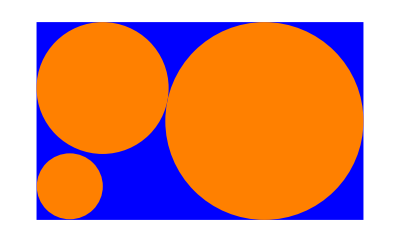

```mathematica
Graphics[{Blue,Rectangle[{0,0},{9.899,6}],Orange,Table[Disk[{x[[i]],y[[i]]},r[[i]]],{i,3}]}]
```

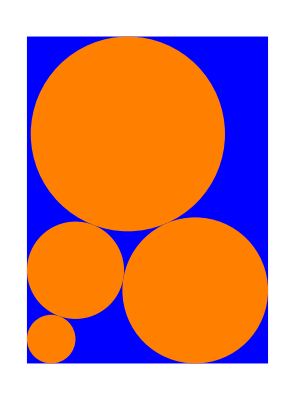

```mathematica
x={1.000,2.000,6.931,4.157};y={1.000,3.828,3.000,9.427};r={1,2,3,4};Graphics[{Blue,Rectangle[{0,0},{9.931,13.427}],Orange,Table[Disk[{x[[i]],y[[i]]},r[[i]]],{i,4}]}]
```

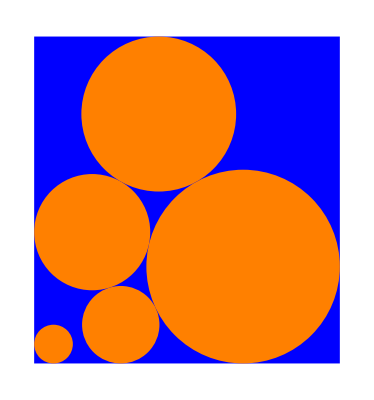

```mathematica
x={1.000,4.476,3.000,6.440,10.800};y={1.000,2.000,6.777,12.874,5.000};r={1,2,3,4,5};Graphics[{Blue,Rectangle[{0,0},{15.8,16.874}],Orange,Table[Disk[{x[[i]],y[[i]]},r[[i]]],{i,Length[r]}]}]
```

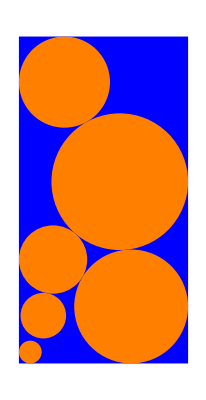

```mathematica
x={1.000,2.144,3.000,4.000,9.857,8.857};y={1.000,4.195,9.121,24.696,5.000,15.954};r={1,2,3,4,5,6};Graphics[{Blue,Rectangle[{0,0},{14.857,28.696}],Orange,Table[Disk[{x[[i]],y[[i]]},r[[i]]],{i,Length[r]}]}]
```

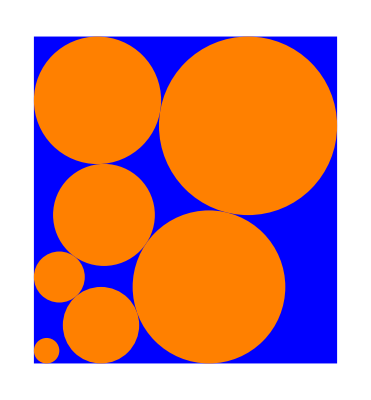

```mathematica
x={1.000,2.000,5.275,5.507,5.000,13.761,16.832};y={1.000,6.778,3.000,11.646,20.632,6.000,18.632};Graphics[{Blue,Rectangle[{0,0},{23.832,25.632}],Orange,Table[Disk[{x[[i]],y[[i]]},i],{i,Length[x]}]}]
```

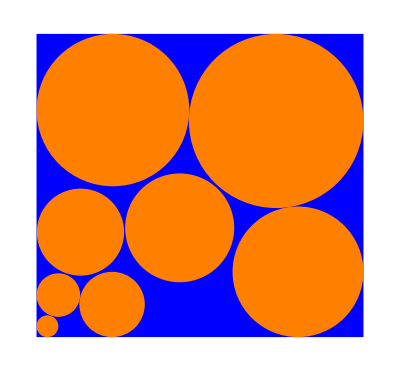

```mathematica
x={1.000,2.000,6.925,4.029,13.122,23.967,7.000,21.967};y={1.000,3.863,3.002,9.645,10.039,6.000,20.856,19.856};Graphics[{Blue,Rectangle[{0,0},{29.967,27.856}],Orange,Table[Disk[{x[[i]],y[[i]]},i],{i,Length[x]}]}]
```

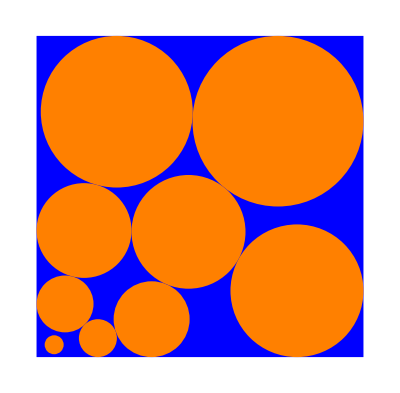

```mathematica
x={1.856,6.460,3.000,12.117,5.000,15.999,27.417,8.446,25.417};y={1.303,2.000,5.610,4.000,13.356,13.216,7.000,25.891,24.891};Graphics[{Blue,Rectangle[{0,0},{34.417,33.891}],Orange,Table[Disk[{x[[i]],y[[i]]},i],{i,Length[x]}]}]
```

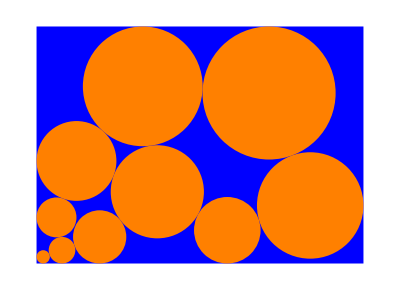

```mathematica
x={1.000,3.828,3.000,9.485,28.661,6.000,18.146,41.116,15.960,34.934};y={1.000,2.000,6.931,4.000,5.000,15.416,10.782,8.727,26.632,25.632};Graphics[{Blue,Rectangle[{0,0},{49.116,35.632}],Orange,Table[Disk[{x[[i]],y[[i]]},i],{i,Length[x]}]}]
```

```mathematica
Problem 3
```

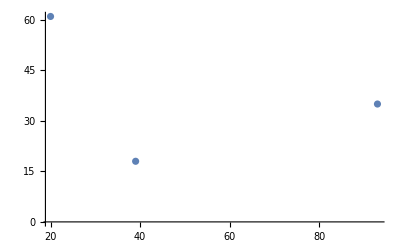

```mathematica
ListPlot[{{20,61},{39,18},{93,35}}]
```

```mathematica
Transpose[{{20,39,93},{61,18,35}}]
```

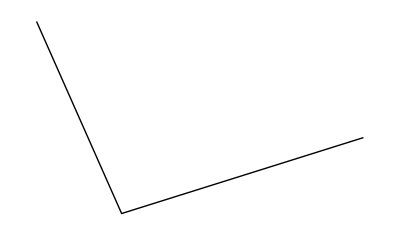

```mathematica
Graphics[Line[{{20,61},{39,18},{93,35}}]]
```

```mathematica
14 15 20 43 51 52
73 40 65 9 94 30
```

```mathematica
Transpose[{{14,15,20,43,51,52},{73,40,65,9,94,30}}]
```

{{14,73},{15,40},{20,65},{43,9},{51,94},{52,30}}

```mathematica
{{{14,73},{20,61}},{{15,40},{20,61}},{{20,65},{20,61}},{{43,9},{39,18}},{{51,94},{20,61}},{{52,30},{39,18}}}//MatrixForm
```

((14
73) | (20
61)
(15
40) | (20
61)
(20
65) | (20
61)
(43
9) | (39
18)
(51
94) | (20
61)
(52
30) | (39
18))

```mathematica
k={{{14,73},{20,61}},{{15,40},{20,61}},{{20,65},{20,61}},{{43,9},{39,18}},{{51,94},{20,61}},{{52,30},{39,18}}}
```

{{{14,73},{20,61}},{{15,40},{20,61}},{{20,65},{20,61}},{{43,9},{39,18}},{{51,94},{20,61}},{{52,30},{39,18}}}

```mathematica
k[[1]]
```

{{14,73},{20,61}}

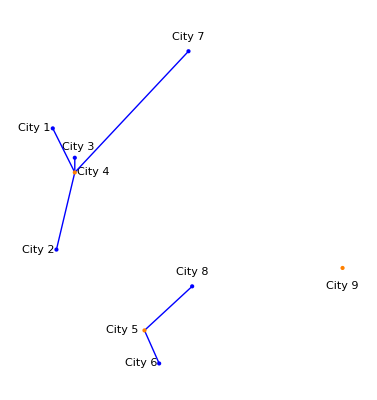

```mathematica
Graphics[{Text["City 1",{9,73}],Text["City 2",{10,40}],Text["City 3",{21,68}],Text["City 6",{38,9}],Text["City 7",{51,98}],Text["City 8",{52,34}],Text["City 4",{25,61}],Text["City 5",{33,18}],Text["City 9",{93,30}],PointSize[Medium],Blue,Point[{{14,73},{15,40},{20,65},{43,9},{51,94},{52,30}}],Line[Table[k[[i]],{i,1,6}]],PointSize[Large],Orange,Point[{{20,61},{39,18},{93,35}}]}]
```